```mathematica
g=9.8; V= 30; th = 50*pi/180;

sol=NDSolve[{x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], x[0] == 0 , x'[0] == V cos[th], y''[t] -g (1 + y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2], y[0] == 2, y'[0] ==  V sin[th]},{x, y}, {t,0,200}];
```

NDSolve::deqn: Equation or list of equations expected instead of -9.8` (1 + SuperscriptBox[ in the first argument SuperscriptBox[x[0] == 0SuperscriptBox[-9.8` (1 + SuperscriptBox[y[0] == 2SuperscriptBox[.

```mathematica
ParametricPlot[{x,y}, {t, 0, 200}]
```

-Graphics-

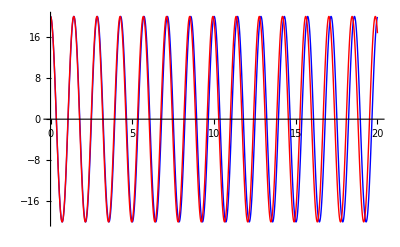

```mathematica
Show[{myplot1,myplot2}]
```

```mathematica
Manipulate[
g=9.8; l=0.5; omega=√(g/l);
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ, {t, 0,20}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]
```